```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/kenneth_levasseur/Documents/active-ads

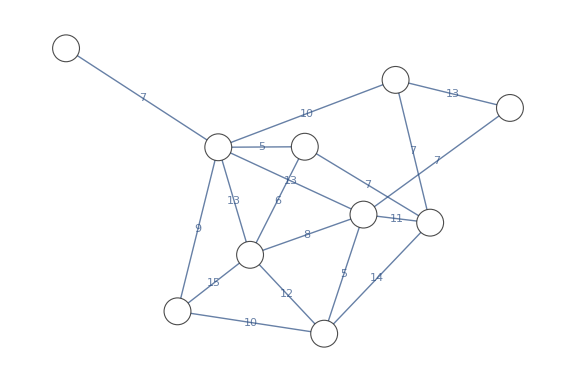

```mathematica
SeedRandom[52];
n=10;e=18;
G=RandomGraph[{n,e},EdgeWeight->RandomInteger[{5,15},e],EdgeLabels->"EdgeWeight",EdgeLabelStyle->Large,VertexLabelStyle->Directive[Italic,18],VertexSize->Large,VertexStyle->White,VertexLabels->Table[i->Placed[ToString[i],Center],{i,1,n}],ImageSize->Large]
```

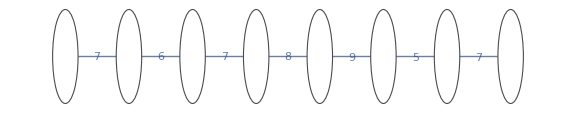

```mathematica
FindSpanningTree[G]
```

```mathematica
GraphEmbedding[G]
```

(1.56223 | 1.62379
0.749255 | 1.25958
1.56107 | 0.363176
2.44074 | 0.992703
0. | 0.995015
0.498848 | 1.98761
0.748872 | 0.726806
0.496831 | 0.)

```mathematica
mstEdges=FindSpanningTree[G]//EdgeList
```

{1<->5,2<->7,3<->8,3<->9,4<->8,5<->9,5<->10,6<->8,7<->9}

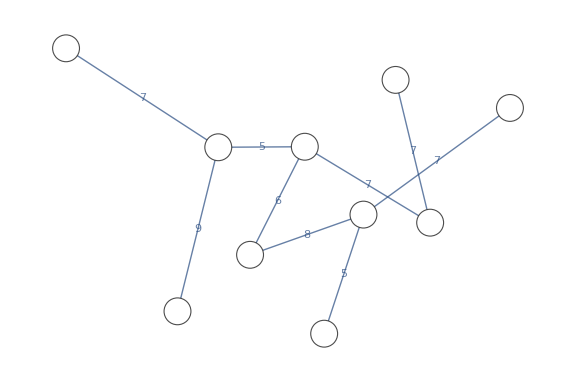

```mathematica
FindSpanningTree[G,VertexCoordinates->GraphEmbedding[G]]
```